```mathematica
(* Computer Graphics with Applications of Dr. Makhanov. *)
```

```mathematica
(* Lecture 2. Animations, Dynamics and Sliders.*)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,VectorPlot, VectorPlot3D,StreamPlot}, ImageSize->Small];
```

```mathematica
(* Parametric Plot in 3D with a "projection" onto x,y-plane *)
```

```mathematica
(* Parametric surface vector-function S4[u,v] in 3D, the components are functions of 2 variables (a,b)*)
```

```mathematica
(* Vector function 1 (surface)  *)
```

```mathematica
x4[a_,b_]:=Cos[b] (6-(5/4+Sin[3 a]) Sin[a-3 b])
```

```mathematica
y4[a_,b_]:=(6-(5/4+Sin[3 a]) Sin[a-3 b]) Sin[b]
```

```mathematica
z4[a_,b_]:= -Cos[a-3 b] (5/4+Sin[3 a])
```

```mathematica
S4[u_,v_]:={x4[u,v],y4[u,v],z4[u,v]}
```

```mathematica
S4small[u_,v_]:={x4[u,v],y4[u,v],z4small[u,v]}
```

```mathematica
P1=ParametricPlot3D[S4[u,v],{u,0,2Pi},{v,0, 2 Pi},PlotStyle->Yellow,  PlotRange->{{-10,10},{-10,10},{-5,3}}]
```

-Graphics3D-

```mathematica
(* Vector function 2 (we flatten the surface and move it down by 5 units)  *)
```

```mathematica
z4small[a_,b_]:= -Cos[a-3 b] (5/4+Sin[3 a])0.01-5
```

```mathematica
P2=ParametricPlot3D[S4small[u,v],{u,0,2Pi},{v,0, 2 Pi},PlotStyle->Brown,MeshStyle->Yellow]
```

-Graphics3D-

```mathematica
Show[P1,P2]
```

-Graphics3D-

```mathematica
(* Space Curve in 3D  *)
```

```mathematica
(* Vector function in 3D (St4[t]) The compunents are functions of 1 variable   *)
```

```mathematica
xt4[u_]:=u Sin[u]
```

```mathematica
yt4[u_]:=Cos[u]
```

```mathematica
zt4[u_]:=u/10
```

```mathematica
(* Vector function *)
```

```mathematica
St4[u_]:={xt4[u],yt4[u],zt4[u]}
```

```mathematica
ParametricPlot3D[St4[u],{u,0,20},BoxRatios->{1,1,1},PlotStyle->{Red,Thick}]
```

-Graphics3D-

```mathematica
(* Example 2 Animate a space curve given by 
xp[u_,n_]:=n/6 u Sin[u]
  yp[u_]:=Cos[u]
  zp[u_]:=u/10
n changes from 1 to 18 u changes from 0 to 20 *)
```

```mathematica
xp[u_,n_]:=n/6u Sin[u]
```

```mathematica
yp[u_]:=Cos[u]
```

```mathematica
zp[u_]:=u/10
```

```mathematica
Spp[u_,n_]:={xp[u,n],yp[u],zp[u]}
```

```mathematica
(* Check whether Spp returns a numerical value (do it at the Labs)  *)
```

```mathematica
Spp[1.,1]
```

{0.140245,0.540302,0.1}

```mathematica
(* Find appropriate BoxRatios. Important! PlotRange must be fixed and can be evaluated only by experiments. 
Manipulate - Similar to Animate with a few additional options and not need to set AnimationRunning->False, {n,1,18}- the animation step is selected automatically  *)
```

```mathematica
Manipulate[ParametricPlot3D[Spp[u,n],{u,0,20},BoxRatios->{1,1,1},PlotPoints->80,PlotRange->{{-60,60},{-1,1},{0,2}},PlotStyle->Thick],{n,1,18}]
```

```mathematica
(* The surfaces produced by Plot3D and ParametricPlot3D can be superimposed. Some new options can be assigned to the function "Show"*)
```

```mathematica
(* Below are Plot3D and ParametricPlot3D superimposed on one graph *)
```

```mathematica
fs15[x_,y_]:=15*Sin[x*y/10]
```

```mathematica
(* P1 is the graph of fs15 *)
```

```mathematica
P1=Plot3D[fs15[x,y] ,{x,0,8},{y,0,8} ,PlotPoints->{15, 15},MeshStyle->Yellow,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
(* Parametric surface *)
```

```mathematica
xd[u_,v_]:=4+(3+Cos[v]) Sin[u]
```

```mathematica
yd[u_,v_]:=4+(3+Cos[v]) Cos[u]
```

```mathematica
zd[u_,v_]:=4+Sin[v]
```

```mathematica
Sd[u_,v_]:={xd[u,v],yd[u,v],zd[u,v]}
```

```mathematica
(* P2 is a graph of Sd *)
```

```mathematica
P2=ParametricPlot3D[Sd[u,v],{u,0,2Pi},{v,0,2Pi},PlotStyle->Green]
```

-Graphics3D-

```mathematica
(* Display a composed graph {P1,P2}. BoxRatios can be evaluated only be experiments *)
```

```mathematica
Show[{P2,P1},BoxRatios->{1,1,0.25}]
```

-Graphics3D-

```mathematica
(* Example 1 Manipulate the space curves. This animates a growing 3D spiral curve with regard to the range {u,0,a} where a is the animation parameter (the growing spiral):{a,1,20} *)
```

```mathematica
xsp2[u_]:=Sin[u]
```

```mathematica
ysp2[u_]:=Cos[u]
```

```mathematica
zsp2[u_]:=u/10
```

```mathematica
Sp2[u_]:={xsp2[u],ysp2[u],zsp2[u]} (* spiral in 3D *)
```

```mathematica
Manipulate[ParametricPlot3D[Sp2[u],{u,0,a},PlotRange->{{-1,1},{-1,1},{0,2}},PlotStyle->{Thickness[0.02], Blue}],{a,1,20}]
```

```mathematica
(* Example 2 Manipulate a 3D plot by two animation parameters: a and b as follows
{a,2,5,0.5} {b,1,10,1} *)
```

```mathematica
fab[x_,y_,a_,b_]:=Sin[a^2* x *y]*Exp[(-x^2-y^2)/b]
```

```mathematica
Manipulate[Plot3D[fab[x,y,a,b],{x,-1,1},{y,-1,1}],{a,2,5,0.5},Delimiter,{b,1,10,1}]
```

```mathematica
(* The function "Table" is similar to a "for" loop in Python   
 1. Table[expr, {Subscript[i, max]}]generates a list of Subscript[i, max] copies of expr
2. Table[expr, {i, Subscript[i, max]}]generates a list of the values of expr when i runs from 1 to Subscript[i, max] with step 1.
3. Table[expr, {i, Subscript[i, min], Subscript[i, max]}]starts with i = Subscript[i, min] ,
with step 1.
  4. Table[expr, {i, Subscript[i, min], Subscript[i, max], di}]uses steps di.
 5. Table[expr, {i, Subscript[i, min], Subscript[i, max]}, {j, Subscript[j, min], Subscript[j, max]}, … ] gives a nested list. *)
```

```mathematica
(* Examples of tables  *)
```

```mathematica
L1=Table[i,{i,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
L1[[2]]
```

2

```mathematica
Lt=Table[i,{i,3,8,0.5}]
```

{3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.}

```mathematica
Lt[[3]]
```

4.

```mathematica
(* Create a list consisting of odd numbers  {3,5,7,9,11,13,15,17}  *)
```

```mathematica
LOddN=Table[2*i+1,{i,8}]
```

{3,5,7,9,11,13,15,17}

```mathematica
(* Length of the List}  *)
```

```mathematica
LL=Length[LOddN]
```

8

```mathematica
(* Create the following list {1^2,2^2,3^2,4^2,5^2,6^2} *)
```

```mathematica
Sqrs=Table[i^2,{i,6}]
```

{1,4,9,16,25,36}

```mathematica
(* Create the following list {4^2,5^2,6^2,7^2,8^2,9^2} *)
```

```mathematica
Sqrs4=Table[i^2,{i,4,9}]
```

{16,25,36,49,64,81}

```mathematica
(* Create the following list {2^2,3^3,4^4,5^5,6^6} *)
```

```mathematica
Pwrs2=Table[i^i,{i,2,6}]
```

{4,27,256,3125,46656}

```mathematica
(* In Mathematica it is possible to create lists of anything. 
Let us create a table of graphs given by 
Plot3D[Sin[x *y-k],{x,0,Pi},{y,0,2*Pi}] for k=1..9 as follows. The Table is a sequence of frames of the animation *)
```

```mathematica
TaG:=Table[Plot3D[Sin[x *y-k],{x,0,Pi},{y,0,2*Pi}],{k,9}]
```

```mathematica
TaG; (*remove the ; *)
```

```mathematica
%47
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Play animation with ListAnimate *)
```

```mathematica
ListAnimate[TaG, AnimationRunning->False]
```

```mathematica
(* Example 1 Using Table to create Animation of Sin[x^2*a]for {a,0.5,1.3,0.1} with x from 0 to 8 *)
```

```mathematica
fsin[x_,a_]:=Sin[x^2*a]
```

```mathematica
Manipulate[Plot[fsin[x,a],{x,0,8}],{a,0.5,1.3,0.1}]
```

```mathematica
T:=Table[Plot[fsin[x,a],{x,0,8}],{a,0.5,1.3,0.1}]
```

```mathematica
ListAnimate[T, AnimationRunning->False]
```

```mathematica
(* Sliders and Dynamics *)
```

```mathematica
(* Am ordinary Mathematica session consists of a series of static inputs and outputs which forms a record of calculations done in the order in which they were executed. However you may often want a fundamentally different kind of output. The one that is automatically updated to always reflect its current value. This new kind of output is provided by the function Dynamic *)
```

```mathematica
(* Compare *)
```

```mathematica
x:=9
```

```mathematica
x
```

9

```mathematica
9
```

9

```mathematica
(* and *)
```

```mathematica
Dynamic[x]
```

```mathematica
Dynamic[x^2]
```

```mathematica
x=3
```

3

```mathematica
(* Slider is used to change the variable s *)
```

```mathematica
Slider[Dynamic[s],{-4,75,3}]
```

```mathematica
s
```

59

```mathematica
(* Dynamic[s] makes the output interactive  *)
```

```mathematica
Dynamic[s]
```

```mathematica
(* The slider below changes "n" from 0 to 100 with the step 2. We also output the Dynamic[n] in the same line using { } *)
```

```mathematica
{Slider[Dynamic[n],{0,100,2}],Dynamic[n]}
```

{,}

```mathematica
(* Example 1 Dynamic graphics. The plot depends he dynamic variable a assigned after the plot is executed  *)
```

```mathematica
f[x_,a_]:=a*x^2
```

```mathematica
Dynamic[Plot[f[x,a],{x,-1,1},PlotRange->{{-1,1},{0,10}}]]
```

```mathematica
{Slider[Dynamic[a],{5,100,2}],Dynamic[a]}
```

{,}

```mathematica
(* Example 2  Use a slider to animate fex2[x_,y_,R1_]:=(x-1/R1)^2+y^2 where R1 is the animation variable changing from 1 to 20 with the step 1. Important! Fix the PlotRange  *)
```

```mathematica
fex2[x_,y_,R1_]:=(x-1/R1)^2+y^2
```

```mathematica
{Slider[Dynamic[R1], {1,20,1}],Dynamic[R1]}
```

{,}

```mathematica
Dynamic[Plot3D[fex2[x,y,R1],{x,-1,1},{y,-1,1},Mesh->True, PlotRange->{Automatic,Automatic,{0,5}},Lighting->Automatic]]
```

```mathematica
(* Example 3: Animate Sin[n3*x]*Exp[-y^2*m3] with 2 sliders m3 and n3 changing from 0 to 10 with step 1 {x,-1,1} {y,-1,1}
Important! Fix the PlotRange. The sliders and the graph are enclosed in { } *)
```

```mathematica
fe4[x_,y_,n3_,m3_]:=Sin[n3*x]*Exp[-y^2*m3]
```

```mathematica
{Slider[Dynamic[m3],{0,10}],Slider[Dynamic[n3],{0,10,1}],Dynamic[Plot3D[fe4[x,y,n3,m3],{x,-1,1} ,{y,-1,1},PlotStyle->Red,Mesh->True,PlotRange->{{-1,1},{-1,1},{-1,1}}]]}
```

{,,}

```mathematica
(* Creating graphic-functions and setting options *)
```

```mathematica
(* Create two animations of  fg1[x_,y_,k_]:=Sin[x *y*k]
for k:=1,2,...10 and for k=6,8,10,...20. 
Set PlotPoints->{40,40},ColorFunction->"Rainbow", PlotStyle->Opacity[0.7] , {x,-1,1},{y,-1,1},AxesLabel->{"x","y","z"},ImageSize->Small or ImageSize->Medium  *)
```

```mathematica
(* Surface function *)
```

```mathematica
fg1[x_,y_,k_]:=Sin[x *y*k/2]+Sin[x*y/4*k]+Sin[x*y/8*k]
```

```mathematica
(* Set common options for Plot3D *)
```

```mathematica
SetOptions[Plot3D, PlotPoints->{20,20},AxesLabel->{"x","y","z"},ImageSize->Small];
```

```mathematica
(* Graphic-function. Animate fg1[x_,y_,k_] for  {x,-2,2},{y,-2,2} 
{k,5,10,1} and {k,5,20,2}  ColorFunction  defines a template of colors *)
```

```mathematica
Plotfg1[k_]:=Plot3D[fg1[x,y,k],{x,-2,2},{y,-2,2},PlotStyle->Opacity[0.7],ColorFunction->"Rainbow",PlotPoints->30]
```

```mathematica
(* Animation 1  *)
```

```mathematica
Manipulate[Plotfg1[k],{k,5,10,1}]
```

```mathematica
(* Animation 2  *)
```

```mathematica
Manipulate[Plotfg1[k],{k,5,20,2}]
```

```mathematica
(* Example 1 Animate 2 surfaces  
    su1[x_,y_,n_]:=n*(x^2 + y^2)/10 (explicit surface)
and a parametric surface 
xu2[u_,v_,n_]:=4 + (3 + Cos[v]) Sin[u]*n
	yu2[u_,v_]:=4 + (3 + Cos[v]) Cos[u]
	zu2[v_]:= 4 + Sin[v] on 1 graph,n is the animation parameter changing from 1 to 5 with the step 0.1.
Fix PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}}),use PlotPoints->40,{x,-4,4},{y,-4,4}{u,-4,4},{v,-4,4} *)
```

```mathematica
(* Define the surfaces *)
```

```mathematica
su1[x_,y_,n_]:=n*(x^2 + y^2)/10
```

```mathematica
xu2[u_,v_,n_]:=4 + (3 + Cos[v]) Sin[u]*n
```

```mathematica
yu2[u_,v_]:=4 + (3 + Cos[v]) Cos[u]
```

```mathematica
zu2[v_]:= 4 + Sin[v]
```

```mathematica
su2[u_,v_,n_]:={xu2[u,v,n],yu2[u,v] ,zu2[v]} (* 3D parametric surface *)
```

```mathematica
(* Define and check the graphics functions *)
```

```mathematica
Plotsu1[n_]:=Plot3D[su1[x,y,n],{x,-4,4},{y,-4,4},PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}},PlotStyle->Blue,Mesh->True, MeshStyle->Yellow]
```

```mathematica
Plotsu2[n_]:=ParametricPlot3D[su2[u,v,n],{u,-4,4},{v,-4,4},PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}},PlotStyle->Red]
```

```mathematica
(* Combined Plot *)
```

```mathematica
Plotsu12[n_]:=Show[{Plotsu2[n],Plotsu1[n]}]
```

```mathematica
(* Play two animations *)
```

```mathematica
Animate[Plotsu12[n],{n,1,5,0.5},AnimationRunning->False]
```

```mathematica
(* If time allows/self study *)
```

```mathematica
(* Two-and Three-Dimensional Vector Fields and Stream Plots (if time allows)  *)
```

```mathematica
(* The procedure VectorPlot depicts a vector field defined by a vector  function (vx(x,y),vy(x,y)). These plots imitate the natural streamflows fields. The first component corresponds to the x component of the vector field  the second function corresponds to the y component. The procedure depicts the vector at every point with the prescribed resolution VectorPoints *)
```

```mathematica
(* We start with 
Example 1 Depict {x^2,x+y} by using the vector field *)
```

```mathematica
(* Define a vector function *)
```

```mathematica
v[x_,y_]:={x^2,x-y^2}
```

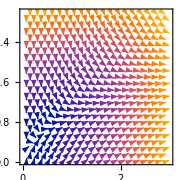

```mathematica
VectorPlot[v[x,y],{x,0,3},{y,0,3},VectorPoints->20,ImageSize->Small]
```

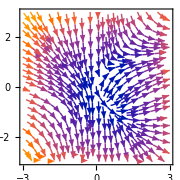

```mathematica
StreamPlot[v[x,y],{x,-3,3},{y,-3,3},ImageSize->Small]
```

```mathematica
(* Example 2 3D vector fields Depict {x^2,x+y*z,xyz} by using the 3D vector field graphics VectorPlot3D*)
```

```mathematica
v3[x_,y_,z_]:={x^2,x+y*z,x*y*z}
```

```mathematica
VectorPlot3D[v3[x,y,z],{x,0,1},{y,0,1},{z,0,1},ImageSize->Small]
```

-Graphics3D-

```mathematica
(* Animating the Vector Fields *)
```

```mathematica
(* Example 3  Create an animation of  a 2D vector field given by {x^2,x-y^2 p/4} with regard to p=1,...15. *)
```

```mathematica
v[x_,y_,p_]:={x^2,x-y^2 p/4}
```

```mathematica
TaVF:=Table[VectorPlot[v[x,y,p],{x,0,3},{y,0,3}],{p,1,15,5}]
```

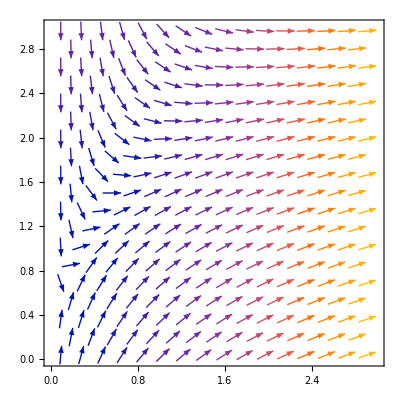
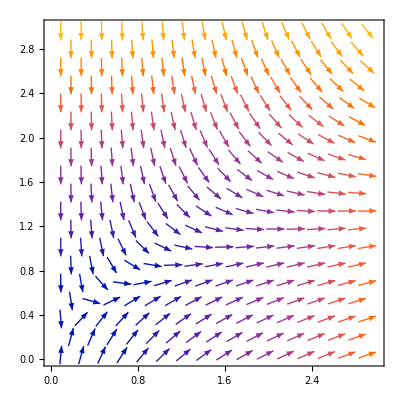
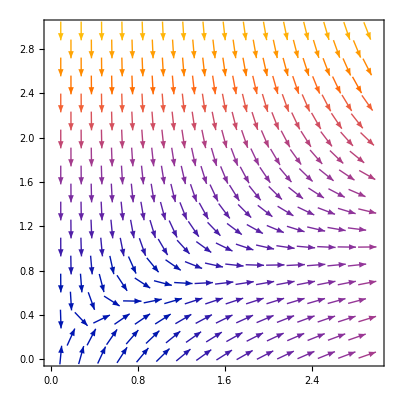

```mathematica
TaVF
```

```mathematica
ListAnimate[TaVF,AnimationRunning->False,ImageSize->Large]
```

```mathematica
(* Beatifying your sliders for professional animations.*)
```

```mathematica
(* Explicit function. a1 - amplitude, n1 -frequiency, p1-shift *)
```

```mathematica
fx[x_,a1_,p1_,n1_]:=a1 Sin[n1 (x+p1)]
```

```mathematica
Manipulate[Plot[fx[x,a1,p1,nn1],{x,0,10},PlotRange->1],{a1,0,1},{p1,0,2Pi},{nn1,1,4}]
```

```mathematica
(* Parametric function Sfxy[x_,a1_,p1_,n1_,a2_,p2_,n2_],a1,p1,n1,a2,p2 and n2 are animation parameters(fx is taken from the example above) *)
```

```mathematica
fy[x_,a2_,p2_,n2_]:=a2 Cos[n2 (x+p2)]
```

```mathematica
Sfxy[x_,a1_,p1_,n1_,a2_,p2_,n2_]:={fx[x,a1,p1,n1],fy[x,a2,p2,n2]}
```

```mathematica
Manipulate[ParametricPlot[Sfxy[x,a1,p1,n1,a2,p2,n2],{x,0,20 Pi},PlotRange->1,PlotPoints->200],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```